## Independence of functional forms

### Intrinsic growth rates - Second power

#### Setup

```mathematica
ClearAll["α",,"β","f"]
```

```mathematica
f[ν_,σ_,ζ_]:=ν NIntegrate[Exp[-x^2/σ^2]Exp[(-(x-ζ)^4)/(81 σ^4)],{x,-Infinity,Infinity}]/NIntegrate[Exp[-x^2/σ^2]^2,{x,-Infinity,Infinity}]
```

#### Dynamics

```mathematica
Subscript[dN, 1]:=Subscript[N, 1](1-S^2/ω^2-(β Subscript[N, 1]+α Subscript[N, 2]));
Subscript[dN, 2]:=Subscript[N, 2](1-(S-ϵ)^2/ω^2-(α Subscript[N, 1]+β Subscript[N, 2]));
dS:=η(-S)Subscript[N, 1]+η(ϵ-S)Subscript[N, 2];
```

```mathematica
Jc:={{D[Subscript[dN, 1],Subscript[N, 1]],D[Subscript[dN, 1],Subscript[N, 2]],D[Subscript[dN, 1],S]},{D[Subscript[dN, 2],Subscript[N, 1]],D[Subscript[dN, 2],Subscript[N, 2]],D[Subscript[dN, 2],S]},{D[dS,Subscript[N, 1]],D[dS,Subscript[N, 2]],D[dS,S]}};
```

#### Phase space

```mathematica
pars={ω->1,σ->1,ν->1,η->1};
ϵs=Range[0,1.5,0.02];
nϵ=Length[ϵs];
ζs=Range[0,6,0.1];
nζ=Length[ζs];
```

```mathematica
eq=Array[,{nζ,nϵ}];
λ1=Array[,{nζ,nϵ}];
λ2=Array[,{nζ,nϵ}];
λ3=Array[,{nζ,nϵ}];
z1=Array[,{nζ,2}];
z2=Array[,{nζ,2}];
z3=Array[,{nζ,2}];
z4=Array[,{nζ,2}];
z5=Array[,{nζ,2}];
z6=Array[,{nζ,2}];
y1=Array[,{nϵ*nζ,2}];
y2=Array[,{nϵ*nζ,2}];
y3=Array[,{nϵ*nζ,2}];
y4=Array[,{nϵ*nζ,2}];
y5=Array[,{nϵ*nζ,2}];
```

```mathematica
eqCounts=List[0,0,0,0,0,0];
```

```mathematica
Do[
ch1=0;
ch2=0;
Do[
α=f[ν/.pars,σ/.pars,ζs[[j1]]];
β=f[ν/.pars,σ/.pars,0];
eq[[j1,j2]]=FullSimplify[Solve[(Subscript[dN, 1]/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]])==0&&(Subscript[dN, 2]/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]])==0&&(dS/.pars/.ϵ->ϵs[[j2]])==0&&Subscript[N, 1]>0&&Subscript[N, 2]>0,{Subscript[N, 1],Subscript[N, 2],S},Reals]];
If[Length[eq[[j1,j2]]]==3,
λ1[[j1,j2]]=Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2,2]]]]];
If[Length[eq[[j1,j2]]]==1,
λ1[[j1,j2]]=Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2]]]]];
λ2[[j1,j2]]=Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.{Subscript[N, 1]->1/β,Subscript[N, 2]->0,S->0}]];
λ3[[j1,j2]]=Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.{Subscript[N, 1]->0,Subscript[N, 2]->1/β,S->ϵs[[j2]]}]];

eqCounts[[Length[eq[[j1,j2]]]+1]]++;

If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]≥0&& λ3[[j1,j2]]≥0,y1[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]<0,y2[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]≥0,y3[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&& λ2[[j1,j2]]>=0&& λ3[[j1,j2]]<0,y4[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[(λ1[[j1,j2]]≥0||λ1[[j1,j2]]==Null[j1,j2])&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]<0,y5[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];

If[λ2[[j1,j2]]<0&&ch1==0,z1[[j1]]={ζs[[j1]],ϵs[[j2]]};ch1=1];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&&λ2[[j1,j2]]<0&&λ3[[j1,j2]]<0&&ch2==0,z2[[j1]]={ζs[[j1]],ϵs[[j2]]};ch2=1],

{j2,nϵ}],
{j1,nζ}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

1 - coex only
2 - coex + s1 + s2
3 - s1
4 - s2
5 - s1 + s2 (priority effect)

```mathematica
eqCounts
```

{0,4411,0,225,0,0}

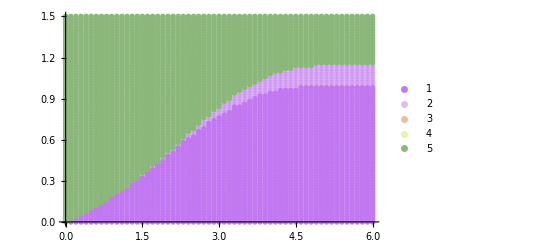

```mathematica
ListPlot[{y1,y2,y3,y4,y5},PlotLegends->Automatic,PlotMarkers->{•,8},PlotStyle->{{ColorData["Pastel",0]},{ColorData["Pastel",0],Opacity[0.5]},{ColorData["Pastel",1/3]},{ColorData["Pastel",2/3]},{ColorData[95,0]}}]
```

```mathematica
f1=Interpolation[z1];
f2=Interpolation[z2];
```

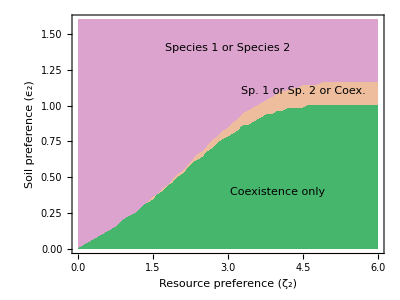

```mathematica
figA2a=RegionPlot[{y>f2[x],y<f2[x],y<f1[x]},{x,0,6},{y,0,1.6},PlotStyle->{RGBColor[0.8570441666666667, 0.6373188333333333, 0.8020406666666666],RGBColor[0.927848, 0.742785, 0.6151383333333333],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]},BoundaryStyle->None,Frame->True,FrameLabel->{"Resource preference (ζ_2)","Soil preference (ϵ_2)"},Axes->{False,False},LabelStyle->{FontSize->20,FontColor->Black},Epilog-> {{Inset[Text[Style["Species 1 or Species 2",FontSize->15]],{3,1.4}],Inset[Text[Style["Sp. 1 or Sp. 2 or Coex. ",FontSize->15]],{4.5,1.1}],Inset[Text[Style["Coexistence only ",FontSize->15]],{4,0.4}]}},AspectRatio->0.75]
```

```mathematica
Export["\\\\wsl.localhost\\Debian\\home\\athma\\trait_cond_models\\paper_2\\images\\figA2a.jpg",figA2a];
```

### Intrinsic growth rates - Fourth power

#### Setup

```mathematica
ClearAll["α","β","f"]
```

```mathematica
f[ν_,σ_,ζ_]:=ν NIntegrate[Exp[-x^2/σ^2]Exp[(-(x-ζ)^4)/(81 σ^4)],{x,-Infinity,Infinity}]/NIntegrate[Exp[-x^2/σ^2]^2,{x,-Infinity,Infinity}]
```

#### Dynamics

```mathematica
Subscript[dN, 1]:=Subscript[N, 1](1-S^4/ω^4-(β Subscript[N, 1]+α Subscript[N, 2]));
Subscript[dN, 2]:=Subscript[N, 2](1-(S-ϵ)^4/ω^4-(α Subscript[N, 1]+β Subscript[N, 2]));
dS:=η(-S)Subscript[N, 1]+η(ϵ-S)Subscript[N, 2];
```

```mathematica
Jc:={{D[Subscript[dN, 1],Subscript[N, 1]],D[Subscript[dN, 1],Subscript[N, 2]],D[Subscript[dN, 1],S]},{D[Subscript[dN, 2],Subscript[N, 1]],D[Subscript[dN, 2],Subscript[N, 2]],D[Subscript[dN, 2],S]},{D[dS,Subscript[N, 1]],D[dS,Subscript[N, 2]],D[dS,S]}};
```

#### Phase space

```mathematica
pars={ω->1,σ->1,ν->1,η->1};
ϵs=Range[0,1.5,0.02];
nϵ=Length[ϵs];
ζs=Range[0,6,0.1];
nζ=Length[ζs];
```

```mathematica
eq=Array[,{nζ,nϵ}];
λ1=Array[,{nζ,nϵ}];
λ2=Array[,{nζ,nϵ}];
λ3=Array[,{nζ,nϵ}];
z1=Array[,{nζ,2}];
z2=Array[,{nζ,2}];
z3=Array[,{nζ,2}];
z4=Array[,{nζ,2}];
z5=Array[,{nζ,2}];
z6=Array[,{nζ,2}];
y1=Array[,{nϵ*nζ,2}];
y2=Array[,{nϵ*nζ,2}];
y3=Array[,{nϵ*nζ,2}];
y4=Array[,{nϵ*nζ,2}];
y5=Array[,{nϵ*nζ,2}];
```

```mathematica
eqCounts=List[0,0,0,0,0,0];
```

```mathematica
Do[
ch1=0;
ch2=0;
Do[
α=f[ν/.pars,σ/.pars,ζs[[j1]]];
β=f[ν/.pars,σ/.pars,0];
eq[[j1,j2]]=FullSimplify[Solve[(Subscript[dN, 1]/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]])==0&&(Subscript[dN, 2]/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]])==0&&(dS/.pars/.ϵ->ϵs[[j2]])==0&&Subscript[N, 1]>0&&Subscript[N, 2]>0,{Subscript[N, 1],Subscript[N, 2],S},Reals]];
If[Length[eq[[j1,j2]]]==3,
λ1[[j1,j2]]=Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2,2]]]]];
If[Length[eq[[j1,j2]]]==1,
λ1[[j1,j2]]=Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2]]]]];
λ2[[j1,j2]]=Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.{Subscript[N, 1]->1/β,Subscript[N, 2]->0,S->0}]];
λ3[[j1,j2]]=Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.{Subscript[N, 1]->0,Subscript[N, 2]->1/β,S->ϵs[[j2]]}]];

eqCounts[[Length[eq[[j1,j2]]]+1]]++;

If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]≥0&& λ3[[j1,j2]]≥0,y1[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]<0,y2[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]≥0,y3[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&& λ2[[j1,j2]]>=0&& λ3[[j1,j2]]<0,y4[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[(λ1[[j1,j2]]≥0||λ1[[j1,j2]]==Null[j1,j2])&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]<0,y5[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];

If[λ2[[j1,j2]]<0&&ch1==0,z1[[j1]]={ζs[[j1]],ϵs[[j2]]};ch1=1];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&&λ2[[j1,j2]]<0&&λ3[[j1,j2]]<0&&ch2==0,z2[[j1]]={ζs[[j1]],ϵs[[j2]]};ch2=1],

{j2,nϵ}],
{j1,nζ}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

1 - coex only
2 - coex + s1 + s2
3 - s1
4 - s2
5 - s1 + s2 (priority effect)

```mathematica
eqCounts
```

{0,3971,0,665,0,0}

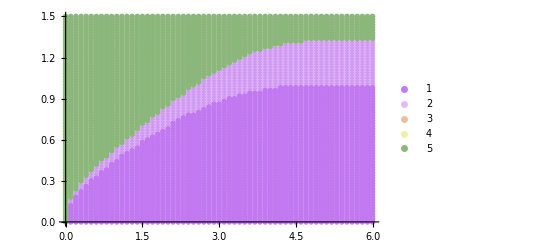

```mathematica
ListPlot[{y1,y2,y3,y4,y5},PlotLegends->Automatic,PlotMarkers->{•,8},PlotStyle->{{ColorData["Pastel",0]},{ColorData["Pastel",0],Opacity[0.5]},{ColorData["Pastel",1/3]},{ColorData["Pastel",2/3]},{ColorData[95,0]}}]
```

```mathematica
f1=Interpolation[z1];
f2=Interpolation[z2];
```

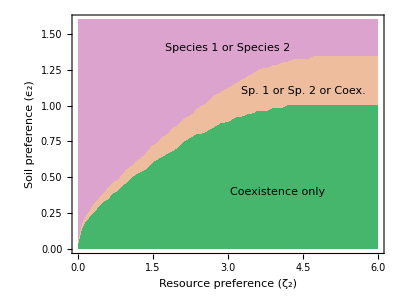

```mathematica
figA2b=RegionPlot[{y>f2[x],y<f2[x],y<f1[x]},{x,0,6},{y,0,1.6},PlotStyle->{RGBColor[0.8570441666666667, 0.6373188333333333, 0.8020406666666666],RGBColor[0.927848, 0.742785, 0.6151383333333333],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]},BoundaryStyle->None,Frame->True,FrameLabel->{"Resource preference (ζ_2)","Soil preference (ϵ_2)"},Axes->{False,False},LabelStyle->{FontSize->20,FontColor->Black},Epilog-> {{Inset[Text[Style["Species 1 or Species 2",FontSize->15]],{3,1.4}],Inset[Text[Style["Sp. 1 or Sp. 2 or Coex. ",FontSize->15]],{4.5,1.1}],Inset[Text[Style["Coexistence only ",FontSize->15]],{4,0.4}]}},AspectRatio->0.75]
```

```mathematica
Export["\\\\wsl.localhost\\Debian\\home\\athma\\trait_cond_models\\paper_2\\images\\figA2b.jpg",figA2b];
```

### Intrinsic growth rates - Eighth power

#### Setup

```mathematica
ClearAll["α","β","f"]
```

```mathematica
f[ν_,σ_,ζ_]:=ν NIntegrate[Exp[-x^2/σ^2]Exp[(-(x-ζ)^4)/(81 σ^4)],{x,-Infinity,Infinity}]/NIntegrate[Exp[-x^2/σ^2]^2,{x,-Infinity,Infinity}]
```

#### Dynamics

```mathematica
Subscript[dN, 1]:=Subscript[N, 1](1-S^8/ω^8-(β Subscript[N, 1]+α Subscript[N, 2]));
Subscript[dN, 2]:=Subscript[N, 2](1-(S-ϵ)^8/ω^8-(α Subscript[N, 1]+β Subscript[N, 2]));
dS:=η(-S)Subscript[N, 1]+η(ϵ-S)Subscript[N, 2];
```

```mathematica
Jc:={{D[Subscript[dN, 1],Subscript[N, 1]],D[Subscript[dN, 1],Subscript[N, 2]],D[Subscript[dN, 1],S]},{D[Subscript[dN, 2],Subscript[N, 1]],D[Subscript[dN, 2],Subscript[N, 2]],D[Subscript[dN, 2],S]},{D[dS,Subscript[N, 1]],D[dS,Subscript[N, 2]],D[dS,S]}};
```

#### Phase space

```mathematica
pars={ω->1,σ->1,ν->1,η->1};
ϵs=Range[0,1.5,0.02];
nϵ=Length[ϵs];
ζs=Range[0,6,0.1];
nζ=Length[ζs];
```

```mathematica
eq=Array[,{nζ,nϵ}];
λ1=Array[,{nζ,nϵ}];
λ2=Array[,{nζ,nϵ}];
λ3=Array[,{nζ,nϵ}];
z1=Array[,{nζ,2}];
z2=Array[,{nζ,2}];
z3=Array[,{nζ,2}];
z4=Array[,{nζ,2}];
z5=Array[,{nζ,2}];
z6=Array[,{nζ,2}];
y1=Array[,{nϵ*nζ,2}];
y2=Array[,{nϵ*nζ,2}];
y3=Array[,{nϵ*nζ,2}];
y4=Array[,{nϵ*nζ,2}];
y5=Array[,{nϵ*nζ,2}];
```

```mathematica
eqCounts=List[0,0,0,0,0,0];
```

```mathematica
Do[
ch1=0;
ch2=0;
Do[
α=f[ν/.pars,σ/.pars,ζs[[j1]]];
β=f[ν/.pars,σ/.pars,0];
eq[[j1,j2]]=FullSimplify[Solve[(Subscript[dN, 1]/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]])==0&&(Subscript[dN, 2]/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]])==0&&(dS/.pars/.ϵ->ϵs[[j2]])==0&&Subscript[N, 1]>0&&Subscript[N, 2]>0,{Subscript[N, 1],Subscript[N, 2],S},Reals]];
If[Length[eq[[j1,j2]]]==3,
λ1[[j1,j2]]=Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2,2]]]]];
If[Length[eq[[j1,j2]]]==1,
λ1[[j1,j2]]=Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2]]]]];
λ2[[j1,j2]]=Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.{Subscript[N, 1]->1/β,Subscript[N, 2]->0,S->0}]];
λ3[[j1,j2]]=Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.{Subscript[N, 1]->0,Subscript[N, 2]->1/β,S->ϵs[[j2]]}]];

eqCounts[[Length[eq[[j1,j2]]]+1]]++;

If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]≥0&& λ3[[j1,j2]]≥0,y1[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]<0,y2[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]≥0,y3[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&& λ2[[j1,j2]]>=0&& λ3[[j1,j2]]<0,y4[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[(λ1[[j1,j2]]≥0||λ1[[j1,j2]]==Null[j1,j2])&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]<0,y5[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];

If[λ2[[j1,j2]]<0&&ch1==0,z1[[j1]]={ζs[[j1]],ϵs[[j2]]};ch1=1];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&&λ2[[j1,j2]]<0&&λ3[[j1,j2]]<0&&ch2==0,z2[[j1]]={ζs[[j1]],ϵs[[j2]]};ch2=1],

{j2,nϵ}],
{j1,nζ}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

1 - coex only
2 - coex + s1 + s2
3 - s1
4 - s2
5 - s1 + s2 (priority effect)

```mathematica
eqCounts
```

{0,3402,0,1234,0,0}

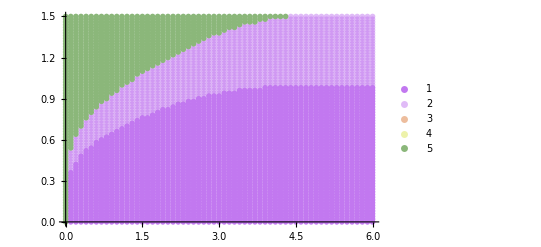

```mathematica
ListPlot[{y1,y2,y3,y4,y5},PlotLegends->Automatic,PlotMarkers->{•,8},PlotStyle->{{ColorData["Pastel",0]},{ColorData["Pastel",0],Opacity[0.5]},{ColorData["Pastel",1/3]},{ColorData["Pastel",2/3]},{ColorData[95,0]}}]
```

```mathematica
f1=Interpolation[z1];
f2=Interpolation[Take[z2,44]];
```

InterpolatingFunction::dmval: Input value {6.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

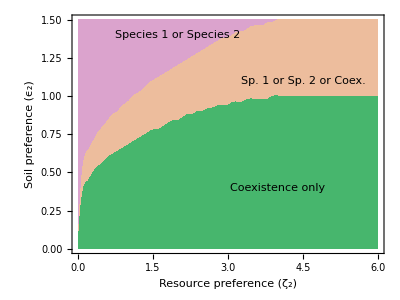

```mathematica
figA2c=RegionPlot[{y>f2[x],y<f2[x],y<f1[x]},{x,0,6},{y,0,1.5},PlotStyle->{RGBColor[0.8570441666666667, 0.6373188333333333, 0.8020406666666666],RGBColor[0.927848, 0.742785, 0.6151383333333333],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]},BoundaryStyle->None,Frame->True,FrameLabel->{"Resource preference (ζ_2)","Soil preference (ϵ_2)"},Axes->{False,False},LabelStyle->{FontSize->20,FontColor->Black},Epilog-> {{Inset[Text[Style["Species 1 or Species 2",FontSize->15]],{2,1.4}],Inset[Text[Style["Sp. 1 or Sp. 2 or Coex. ",FontSize->15]],{4.5,1.1}],Inset[Text[Style["Coexistence only ",FontSize->15]],{4,0.4}]}},AspectRatio->0.75]
```

```mathematica
Export["\\\\wsl.localhost\\Debian\\home\\athma\\trait_cond_models\\paper_2\\images\\figA2c.jpg",figA2c];
```

### Competition coefficient - Narrow total utilization curve δ=1

#### Setup

```mathematica
ClearAll["α","β","f"]
```

```mathematica
f[ν_,σ_,ζ_]:=ν NIntegrate[Exp[-x^2/σ^2]Exp[(-(x-ζ)^4)/σ^4],{x,-Infinity,Infinity}]/NIntegrate[Exp[-x^2/σ^2]^2,{x,-Infinity,Infinity}]
```

#### Dynamics

```mathematica
Subscript[dN, 1]:=Subscript[N, 1](1-S^4/ω^4-(β Subscript[N, 1]+α Subscript[N, 2]));
Subscript[dN, 2]:=Subscript[N, 2](1-(S-ϵ)^4/ω^4-(α Subscript[N, 1]+β Subscript[N, 2]));
dS:=η(-S)Subscript[N, 1]+η(ϵ-S)Subscript[N, 2];
```

```mathematica
Jc:={{D[Subscript[dN, 1],Subscript[N, 1]],D[Subscript[dN, 1],Subscript[N, 2]],D[Subscript[dN, 1],S]},{D[Subscript[dN, 2],Subscript[N, 1]],D[Subscript[dN, 2],Subscript[N, 2]],D[Subscript[dN, 2],S]},{D[dS,Subscript[N, 1]],D[dS,Subscript[N, 2]],D[dS,S]}};
```

#### Phase space

```mathematica
pars={ω->1,σ->1,ν->1,η->1};
ϵs=Range[0,1.5,0.02];
nϵ=Length[ϵs];
ζs=Range[0,6,0.1];
nζ=Length[ζs];
```

```mathematica
eq=Array[,{nζ,nϵ}];
λ1=Array[,{nζ,nϵ}];
λ2=Array[,{nζ,nϵ}];
λ3=Array[,{nζ,nϵ}];
z1=Array[,{nζ,2}];
z2=Array[,{nζ,2}];
z3=Array[,{nζ,2}];
z4=Array[,{nζ,2}];
z5=Array[,{nζ,2}];
z6=Array[,{nζ,2}];
y1=Array[,{nϵ*nζ,2}];
y2=Array[,{nϵ*nζ,2}];
y3=Array[,{nϵ*nζ,2}];
y4=Array[,{nϵ*nζ,2}];
y5=Array[,{nϵ*nζ,2}];
```

```mathematica
eqCounts=List[0,0,0,0,0,0];
```

```mathematica
Do[
ch1=0;
ch2=0;
Do[
α=f[ν/.pars,σ/.pars,ζs[[j1]]];
β=f[ν/.pars,σ/.pars,0];
eq[[j1,j2]]=FullSimplify[Solve[(Subscript[dN, 1]/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]])==0&&(Subscript[dN, 2]/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]])==0&&(dS/.pars/.ϵ->ϵs[[j2]])==0&&Subscript[N, 1]>0&&Subscript[N, 2]>0,{Subscript[N, 1],Subscript[N, 2],S},Reals]];
If[Length[eq[[j1,j2]]]==3,
λ1[[j1,j2]]=Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2,2]]]]];
If[Length[eq[[j1,j2]]]==1,
λ1[[j1,j2]]=Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2]]]]];
λ2[[j1,j2]]=Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.{Subscript[N, 1]->1/β,Subscript[N, 2]->0,S->0}]];
λ3[[j1,j2]]=Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.{Subscript[N, 1]->0,Subscript[N, 2]->1/β,S->ϵs[[j2]]}]];

eqCounts[[Length[eq[[j1,j2]]]+1]]++;

If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]≥0&& λ3[[j1,j2]]≥0,y1[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]<0,y2[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]≥0,y3[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&& λ2[[j1,j2]]>=0&& λ3[[j1,j2]]<0,y4[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[(λ1[[j1,j2]]≥0||λ1[[j1,j2]]==Null[j1,j2])&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]<0,y5[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];

If[λ2[[j1,j2]]<0&&ch1==0,z1[[j1]]={ζs[[j1]],ϵs[[j2]]};ch1=1];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&&λ2[[j1,j2]]<0&&λ3[[j1,j2]]<0&&ch2==0,z2[[j1]]={ζs[[j1]],ϵs[[j2]]};ch2=1],

{j2,nϵ}],
{j1,nζ}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

1 - coex only
2 - coex + s1 + s2
3 - s1
4 - s2
5 - s1 + s2 (priority effect)

```mathematica
eqCounts
```

{0,3762,0,874,0,0}

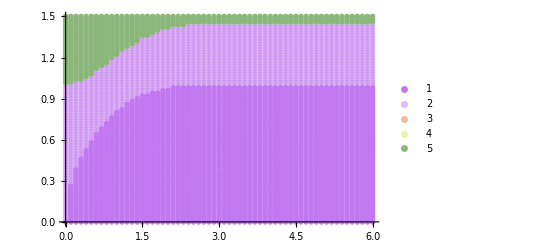

```mathematica
ListPlot[{y1,y2,y3,y4,y5},PlotLegends->Automatic,PlotMarkers->{•,8},PlotStyle->{{ColorData["Pastel",0]},{ColorData["Pastel",0],Opacity[0.5]},{ColorData["Pastel",1/3]},{ColorData["Pastel",2/3]},{ColorData[95,0]}}]
```

```mathematica
f1=Interpolation[z1];
f2=Interpolation[z2];
```

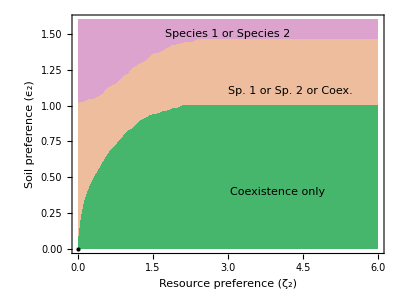

```mathematica
figA3a=RegionPlot[{y>f2[x],y<f2[x],y<f1[x]},{x,0,6},{y,0,1.6},PlotStyle->{RGBColor[0.8570441666666667, 0.6373188333333333, 0.8020406666666666],RGBColor[0.927848, 0.742785, 0.6151383333333333],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]},BoundaryStyle->None,Frame->True,FrameLabel->{"Resource preference (ζ_2)","Soil preference (ϵ_2)"},Axes->{False,False},LabelStyle->{FontSize->20,FontColor->Black},Epilog-> {{PointSize[Large],Point[{0,0}]},{Inset[Text[Style["Species 1 or Species 2",FontSize->15]],{3,1.5}],Inset[Text[Style["Sp. 1 or Sp. 2 or Coex. ",FontSize->15]],{4.25,1.1}],Inset[Text[Style["Coexistence only ",FontSize->15]],{4,0.4}]}},AspectRatio->0.75]
```

```mathematica
Export["\\\\wsl.localhost\\Debian\\home\\athma\\trait_cond_models\\paper_2\\images\\figA3a.jpg",figA3a];
```

### Competition coefficient - Intermediate total utilization curve δ=2

#### Setup

```mathematica
ClearAll["α","β","f"]
```

```mathematica
f[ν_,σ_,ζ_]:=ν NIntegrate[Exp[-x^2/σ^2]Exp[(-(x-ζ)^4)/(16 σ^4)],{x,-Infinity,Infinity}]/NIntegrate[Exp[-x^2/σ^2]^2,{x,-Infinity,Infinity}]
```

#### Dynamics

```mathematica
Subscript[dN, 1]:=Subscript[N, 1](1-S^4/ω^4-(β Subscript[N, 1]+α Subscript[N, 2]));
Subscript[dN, 2]:=Subscript[N, 2](1-(S-ϵ)^4/ω^4-(α Subscript[N, 1]+β Subscript[N, 2]));
dS:=η(-S)Subscript[N, 1]+η(ϵ-S)Subscript[N, 2];
```

```mathematica
Jc:={{D[Subscript[dN, 1],Subscript[N, 1]],D[Subscript[dN, 1],Subscript[N, 2]],D[Subscript[dN, 1],S]},{D[Subscript[dN, 2],Subscript[N, 1]],D[Subscript[dN, 2],Subscript[N, 2]],D[Subscript[dN, 2],S]},{D[dS,Subscript[N, 1]],D[dS,Subscript[N, 2]],D[dS,S]}};
```

#### Phase space

```mathematica
pars={ω->1,σ->1,ν->1,η->1};
ϵs=Range[0,1.5,0.02];
nϵ=Length[ϵs];
ζs=Range[0,6,0.1];
nζ=Length[ζs];
```

```mathematica
eq=Array[,{nζ,nϵ}];
λ1=Array[,{nζ,nϵ}];
λ11=Array[,{nζ,nϵ}];
λ12=Array[,{nζ,nϵ}];
λ2=Array[,{nζ,nϵ}];
λ3=Array[,{nζ,nϵ}];
z1=Array[,{nζ,2}];
z2=Array[,{nζ,2}];
z3=Array[,{nζ,2}];
y1=Array[,{nϵ*nζ,2}];
y2=Array[,{nϵ*nζ,2}];
y3=Array[,{nϵ*nζ,2}];
y4=Array[,{nϵ*nζ,2}];
y5=Array[,{nϵ*nζ,2}];
y6=Array[,{nϵ*nζ,2}];
y7=Array[,{nϵ*nζ,2}];

eqCounts=List[0,0,0,0,0,0];
```

```mathematica
Timing[
Do[
ch1=0;
ch2=0;
ch3=0;
Do[
α=f[ν/.pars,σ/.pars,ζs[[j1]]];
β=f[ν/.pars,σ/.pars,0];
eq[[j1,j2]]=FullSimplify[Solve[(Subscript[dN, 1]/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]])==0&&(Subscript[dN, 2]/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]])==0&&(dS/.pars/.ϵ->ϵs[[j2]])==0&&Subscript[N, 1]>0&&Subscript[N, 2]>0,{Subscript[N, 1],Subscript[N, 2],S},Reals]];

If[Length[eq[[j1,j2]]]==3,
λ1[[j1,j2]]=Max[Re[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2,2]]]]]];

If[Length[eq[[j1,j2]]]==2,
λ11[[j1,j2]]=Max[Re[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2,1]]]]];
λ12[[j1,j2]]=Max[Re[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2,2]]]]];
λ1[[j1,j2]]=Min[λ11[[j1,j2]],λ12[[j1,j2]]];
If[λ11[[j1,j2]]<0&&λ12[[j1,j2]]<0,multiCoex++]];

If[Length[eq[[j1,j2]]]==1,
λ1[[j1,j2]]=Max[Re[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2]]]]]];

λ2[[j1,j2]]=Max[Re[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.{Subscript[N, 1]->1/β,Subscript[N, 2]->0,S->0}]]];

λ3[[j1,j2]]=Max[Re[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.{Subscript[N, 1]->0,Subscript[N, 2]->1/β,S->ϵs[[j2]]}]]];

eqCounts[[Min[Length[eq[[j1,j2]]],5]+1]]++;

If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]≥0&& λ3[[j1,j2]]≥0,y1[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]<0,y2[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]≥0,y3[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&& λ2[[j1,j2]]>=0&& λ3[[j1,j2]]<0,y4[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]<0,y5[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]>=0,y6[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]>=0&& λ3[[j1,j2]]<0,y7[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];

If[λ2[[j1,j2]]<0&&ch1==0,z1[[j1]]={ζs[[j1]],ϵs[[j2]]};ch1=1];
If[λ3[[j1,j2]]<0&&ch2==0,z2[[j1]]={ζs[[j1]],ϵs[[j2]]};ch2=1];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&&ch3==0,z3[[j1]]={ζs[[j1]],ϵs[[j2]]};ch3=1],

{j2,nϵ}],
{j1,nζ}]
]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

{42.375,Null}

1 - coex only
2 - coex + s1 + s2
3 - s1
4 - s2
5 - s1 + s2 (priority effect)

```mathematica
eqCounts
```

{0,3859,0,777,0,0}

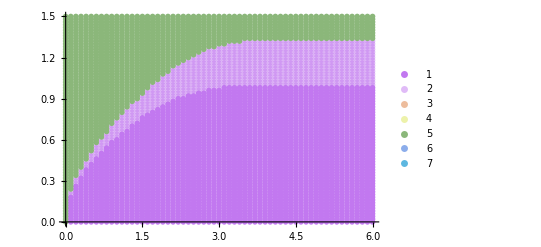

```mathematica
ListPlot[{y1,y2,y3,y4,y5,y6,y7},PlotLegends->Automatic,PlotMarkers->{•,8},PlotStyle->{{ColorData["Pastel",0]},{ColorData["Pastel",0],Opacity[0.5]},{ColorData["Pastel",1/3]},{ColorData["Pastel",2/3]},{ColorData[95,0]},ColorData[95,1],ColorData[95,6]}]
```

```mathematica
f1=Interpolation[z1];
f2=Interpolation[z3];
```

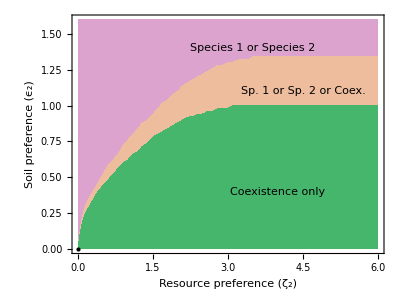

```mathematica
figA3b=RegionPlot[{y>f2[x],y<f2[x],y<f1[x]},{x,0,6},{y,0,1.6},PlotStyle->{RGBColor[0.8570441666666667, 0.6373188333333333, 0.8020406666666666],RGBColor[0.927848, 0.742785, 0.6151383333333333],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]},BoundaryStyle->None,Frame->True,FrameLabel->{"Resource preference (ζ_2)","Soil preference (ϵ_2)"},Axes->{False,False},LabelStyle->{FontSize->20,FontColor->Black},Epilog-> {{{PointSize[Large],Point[{0,0}]},Inset[Text[Style["Species 1 or Species 2",FontSize->15]],{3.5,1.4}],Inset[Text[Style["Sp. 1 or Sp. 2 or Coex. ",FontSize->15]],{4.5,1.1}],Inset[Text[Style["Coexistence only ",FontSize->15]],{4,0.4}]}},AspectRatio->0.75]
```

```mathematica
Export["\\\\wsl.localhost\\Debian\\home\\athma\\trait_cond_models\\paper_2\\images\\figA3b.jpg",figA3b];
```

### Competition coefficient - Wide total utilization curve δ=3

#### Setup

```mathematica
ClearAll["α","β","f"]
```

```mathematica
f[ν_,σ_,ζ_]:=ν NIntegrate[Exp[-x^2/σ^2]Exp[(-(x-ζ)^4)/(81 σ^4)],{x,-Infinity,Infinity}]/NIntegrate[Exp[-x^2/σ^2]^2,{x,-Infinity,Infinity}]
```

#### Dynamics

```mathematica
Subscript[dN, 1]:=Subscript[N, 1](1-S^4/ω^4-(β Subscript[N, 1]+α Subscript[N, 2]));
Subscript[dN, 2]:=Subscript[N, 2](1-(S-ϵ)^4/ω^4-(α Subscript[N, 1]+β Subscript[N, 2]));
dS:=η(-S)Subscript[N, 1]+η(ϵ-S)Subscript[N, 2];
```

```mathematica
Jc:={{D[Subscript[dN, 1],Subscript[N, 1]],D[Subscript[dN, 1],Subscript[N, 2]],D[Subscript[dN, 1],S]},{D[Subscript[dN, 2],Subscript[N, 1]],D[Subscript[dN, 2],Subscript[N, 2]],D[Subscript[dN, 2],S]},{D[dS,Subscript[N, 1]],D[dS,Subscript[N, 2]],D[dS,S]}};
```

#### Phase space

```mathematica
pars={ω->1,σ->1,ν->1,η->1};
ϵs=Range[0,1.5,0.02];
nϵ=Length[ϵs];
ζs=Range[0,6,0.1];
nζ=Length[ζs];
```

```mathematica
eq=Array[,{nζ,nϵ}];
λ1=Array[,{nζ,nϵ}];
λ11=Array[,{nζ,nϵ}];
λ12=Array[,{nζ,nϵ}];
λ2=Array[,{nζ,nϵ}];
λ3=Array[,{nζ,nϵ}];
z1=Array[,{nζ,2}];
z2=Array[,{nζ,2}];
z3=Array[,{nζ,2}];
y1=Array[,{nϵ*nζ,2}];
y2=Array[,{nϵ*nζ,2}];
y3=Array[,{nϵ*nζ,2}];
y4=Array[,{nϵ*nζ,2}];
y5=Array[,{nϵ*nζ,2}];
y6=Array[,{nϵ*nζ,2}];
y7=Array[,{nϵ*nζ,2}];

eqCounts=List[0,0,0,0,0,0];
```

```mathematica
Timing[
Do[
ch1=0;
ch2=0;
ch3=0;
Do[
α=f[ν/.pars,σ/.pars,ζs[[j1]]];
β=f[ν/.pars,σ/.pars,0];
eq[[j1,j2]]=FullSimplify[Solve[(Subscript[dN, 1]/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]])==0&&(Subscript[dN, 2]/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]])==0&&(dS/.pars/.ϵ->ϵs[[j2]])==0&&Subscript[N, 1]>0&&Subscript[N, 2]>0,{Subscript[N, 1],Subscript[N, 2],S},Reals]];

If[Length[eq[[j1,j2]]]==3,
λ1[[j1,j2]]=Max[Re[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2,2]]]]]];

If[Length[eq[[j1,j2]]]==2,
λ11[[j1,j2]]=Max[Re[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2,1]]]]];
λ12[[j1,j2]]=Max[Re[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2,2]]]]];
λ1[[j1,j2]]=Min[λ11[[j1,j2]],λ12[[j1,j2]]];
If[λ11[[j1,j2]]<0&&λ12[[j1,j2]]<0,multiCoex++]];

If[Length[eq[[j1,j2]]]==1,
λ1[[j1,j2]]=Max[Re[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2]]]]]];

λ2[[j1,j2]]=Max[Re[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.{Subscript[N, 1]->1/β,Subscript[N, 2]->0,S->0}]]];

λ3[[j1,j2]]=Max[Re[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.{Subscript[N, 1]->0,Subscript[N, 2]->1/β,S->ϵs[[j2]]}]]];

eqCounts[[Min[Length[eq[[j1,j2]]],5]+1]]++;

If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]≥0&& λ3[[j1,j2]]≥0,y1[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]<0,y2[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]≥0,y3[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&& λ2[[j1,j2]]>=0&& λ3[[j1,j2]]<0,y4[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]<0,y5[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]>=0,y6[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]>=0&& λ3[[j1,j2]]<0,y7[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];

If[λ2[[j1,j2]]<0&&ch1==0,z1[[j1]]={ζs[[j1]],ϵs[[j2]]};ch1=1];
If[λ3[[j1,j2]]<0&&ch2==0,z2[[j1]]={ζs[[j1]],ϵs[[j2]]};ch2=1];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&&ch3==0,z3[[j1]]={ζs[[j1]],ϵs[[j2]]};ch3=1],

{j2,nϵ}],
{j1,nζ}]
]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

{43.2656,Null}

1 - coex only
2 - coex + s1 + s2
3 - s1
4 - s2
5 - s1 + s2 (priority effect)

```mathematica
eqCounts
```

{0,3971,0,665,0,0}

```mathematica
ListPlot[{y1,y2,y3,y4,y5,y6,y7},PlotLegends->Automatic,PlotMarkers->{•,8},PlotStyle->{{ColorData["Pastel",0]},{ColorData["Pastel",0],Opacity[0.5]},{ColorData["Pastel",1/3]},{ColorData["Pastel",2/3]},{ColorData[95,0]}}]
```

-Graphics-

```mathematica
f1=Interpolation[z1];
f2=Interpolation[z3];
```

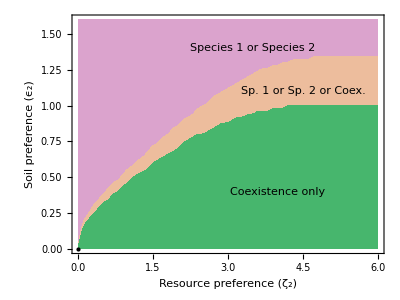

```mathematica
figA3c=RegionPlot[{y>f2[x],y<f2[x],y<f1[x]},{x,0,6},{y,0,1.6},PlotStyle->{RGBColor[0.8570441666666667, 0.6373188333333333, 0.8020406666666666],RGBColor[0.927848, 0.742785, 0.6151383333333333],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]},BoundaryStyle->None,Frame->True,FrameLabel->{"Resource preference (ζ_2)","Soil preference (ϵ_2)"},Axes->{False,False},LabelStyle->{FontSize->20,FontColor->Black},Epilog-> {{PointSize[Large],Point[{0,0}]},{Inset[Text[Style["Species 1 or Species 2",FontSize->13]],{3.5,1.4}],Inset[Text[Style["Sp. 1 or Sp. 2 or Coex. ",FontSize->13]],{4.5,1.1}],Inset[Text[Style["Coexistence only ",FontSize->13]],{4,0.4}]}},AspectRatio->0.75]
```

```mathematica
Export["\\\\wsl.localhost\\Debian\\home\\athma\\trait_cond_models\\paper_2\\images\\figA3c.jpg",figA3c];
```

### Competition coefficient - Absolute value of trait difference

```mathematica
ClearAll["α","β","f"]
```

#### Dynamics

```mathematica
Subscript[dN, 1]:=Subscript[N, 1](1-S^4/ω^4-(β Subscript[N, 1]+α Subscript[N, 2]));
Subscript[dN, 2]:=Subscript[N, 2](1-(S-ϵ)^4/ω^4-(α Subscript[N, 1]+β Subscript[N, 2]));
dS:=η(-S)Subscript[N, 1]+η(ϵ-S)Subscript[N, 2];
```

```mathematica
Jc:={{D[Subscript[dN, 1],Subscript[N, 1]],D[Subscript[dN, 1],Subscript[N, 2]],D[Subscript[dN, 1],S]},{D[Subscript[dN, 2],Subscript[N, 1]],D[Subscript[dN, 2],Subscript[N, 2]],D[Subscript[dN, 2],S]},{D[dS,Subscript[N, 1]],D[dS,Subscript[N, 2]],D[dS,S]}};
```

#### Phase space

```mathematica
pars={ω->1,σ->1,ν->1,η->1};
ϵs=Range[0,1.5,0.02];
nϵ=Length[ϵs];
ζs=Range[0,4,0.1];
nζ=Length[ζs];
```

```mathematica
eq=Array[,{nζ,nϵ}];
λ1=Array[,{nζ,nϵ}];
λ2=Array[,{nζ,nϵ}];
λ3=Array[,{nζ,nϵ}];
z1=Array[,{nζ,2}];
z2=Array[,{nζ,2}];
z3=Array[,{nζ,2}];
z4=Array[,{nζ,2}];
z5=Array[,{nζ,2}];
z6=Array[,{nζ,2}];
y1=Array[,{nϵ*nζ,2}];
y2=Array[,{nϵ*nζ,2}];
y3=Array[,{nϵ*nζ,2}];
y4=Array[,{nϵ*nζ,2}];
y5=Array[,{nϵ*nζ,2}];
```

```mathematica
eqCounts=List[0,0,0,0,0,0];
```

```mathematica
Do[
ch1=0;
ch2=0;
Do[
α=ν Exp[-ζ/(2σ)]/.pars/.ζ->ζs[[j1]];
β=ν/.pars;
eq[[j1,j2]]=FullSimplify[Solve[(Subscript[dN, 1]/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]])==0&&(Subscript[dN, 2]/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]])==0&&(dS/.pars/.ϵ->ϵs[[j2]])==0&&Subscript[N, 1]>0&&Subscript[N, 2]>0,{Subscript[N, 1],Subscript[N, 2],S},Reals]];
If[Length[eq[[j1,j2]]]==3,
λ1[[j1,j2]]=Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2,2]]]]];
If[Length[eq[[j1,j2]]]==1,
λ1[[j1,j2]]=Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2]]]]];
λ2[[j1,j2]]=Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.{Subscript[N, 1]->1/β,Subscript[N, 2]->0,S->0}]];
λ3[[j1,j2]]=Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.{Subscript[N, 1]->0,Subscript[N, 2]->1/β,S->ϵs[[j2]]}]];

eqCounts[[Length[eq[[j1,j2]]]+1]]++;

If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]≥0&& λ3[[j1,j2]]≥0,y1[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]<0,y2[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]≥0,y3[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&& λ2[[j1,j2]]>=0&& λ3[[j1,j2]]<0,y4[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[(λ1[[j1,j2]]≥0||λ1[[j1,j2]]==Null[j1,j2])&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]<0,y5[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];

If[λ2[[j1,j2]]<0&&ch1==0,z1[[j1]]={ζs[[j1]],ϵs[[j2]]};ch1=1];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&&λ2[[j1,j2]]<0&&λ3[[j1,j2]]<0&&ch2==0,z2[[j1]]={ζs[[j1]],ϵs[[j2]]};ch2=1],

{j2,nϵ}],
{j1,nζ}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Solve::svars: Equations may not give solutions for all "solve" variables.

Eigenvalues::eival: Unable to find all roots of the characteristic polynomial.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

1 - coex only
2 - coex + s1 + s2
3 - s1
4 - s2
5 - s1 + s2 (priority effect)

```mathematica
eqCounts
```

{0,2652,0,464,0,0}

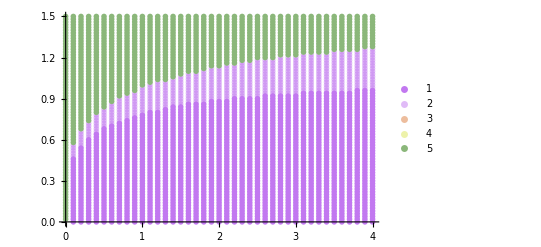

```mathematica
ListPlot[{y1,y2,y3,y4,y5},PlotLegends->Automatic,PlotMarkers->{•,8},PlotStyle->{{ColorData["Pastel",0]},{ColorData["Pastel",0],Opacity[0.5]},{ColorData["Pastel",1/3]},{ColorData["Pastel",2/3]},{ColorData[95,0]}}]
```

```mathematica
f1=Interpolation[z1];
f2=Interpolation[z2];
```

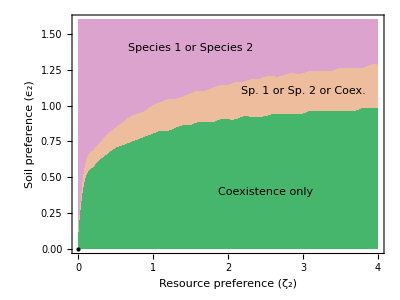

```mathematica
figA4a=RegionPlot[{y>f2[x],y<f2[x],y<f1[x]},{x,0,4},{y,0,1.6},PlotStyle->{RGBColor[0.8570441666666667, 0.6373188333333333, 0.8020406666666666],RGBColor[0.927848, 0.742785, 0.6151383333333333],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]},BoundaryStyle->None,Frame->True,FrameLabel->{"Resource preference (ζ_2)","Soil preference (ϵ_2)"},Axes->{False,False},LabelStyle->{FontSize->20,FontColor->Black},Epilog-> {{PointSize[Large],Point[{0,0}]},{Inset[Text[Style["Species 1 or Species 2",FontSize->13]],{1.5,1.4}],Inset[Text[Style["Sp. 1 or Sp. 2 or Coex. ",FontSize->13]],{3,1.1}],Inset[Text[Style["Coexistence only ",FontSize->13]],{2.5,0.4}]}},AspectRatio->0.75]
```

```mathematica
Export["\\\\wsl.localhost\\Debian\\home\\athma\\trait_cond_models\\paper_2\\images\\figA4a.jpg",figA4a];
```

### Competition coefficient - Quadratic total utilization ~ Quadratic function of trait difference

#### Setup

```mathematica
ClearAll["α","β","f"]
```

```mathematica
ν Integrate[Exp[-x^2/σ^2]Exp[(-(x-ζ)^2)/σ^2],{x,-Infinity,Infinity},Assumptions->σ>0]/Integrate[Exp[-x^2/σ^2]^2,{x,-Infinity,Infinity},Assumptions->σ>0]
```

ⅇ^(-ζ^2/(2 σ^2)) ν

```mathematica
ν Integrate[Exp[-x^2/σ^2]Exp[-x^2/σ^2],{x,-Infinity,Infinity},Assumptions->σ>0]/Integrate[Exp[-x^2/σ^2]^2,{x,-Infinity,Infinity},Assumptions->σ>0]
```

ν

#### Dynamics

```mathematica
Subscript[dN, 1]:=Subscript[N, 1](1-S^4/ω^4-(β Subscript[N, 1]+α Subscript[N, 2]));
Subscript[dN, 2]:=Subscript[N, 2](1-(S-ϵ)^4/ω^4-(α Subscript[N, 1]+β Subscript[N, 2]));
dS:=η(-S)Subscript[N, 1]+η(ϵ-S)Subscript[N, 2];
```

```mathematica
Jc:={{D[Subscript[dN, 1],Subscript[N, 1]],D[Subscript[dN, 1],Subscript[N, 2]],D[Subscript[dN, 1],S]},{D[Subscript[dN, 2],Subscript[N, 1]],D[Subscript[dN, 2],Subscript[N, 2]],D[Subscript[dN, 2],S]},{D[dS,Subscript[N, 1]],D[dS,Subscript[N, 2]],D[dS,S]}};
```

#### Phase space

```mathematica
pars={ω->1,σ->1,ν->1,η->1};
ϵs=Range[0,1.5,0.02];
nϵ=Length[ϵs];
ζs=Range[0,4,0.1];
nζ=Length[ζs];
```

```mathematica
eq=Array[,{nζ,nϵ}];
λ1=Array[,{nζ,nϵ}];
λ2=Array[,{nζ,nϵ}];
λ3=Array[,{nζ,nϵ}];
z1=Array[,{nζ,2}];
z2=Array[,{nζ,2}];
z3=Array[,{nζ,2}];
z4=Array[,{nζ,2}];
z5=Array[,{nζ,2}];
z6=Array[,{nζ,2}];
y1=Array[,{nϵ*nζ,2}];
y2=Array[,{nϵ*nζ,2}];
y3=Array[,{nϵ*nζ,2}];
y4=Array[,{nϵ*nζ,2}];
y5=Array[,{nϵ*nζ,2}];
```

```mathematica
eqCounts=List[0,0,0,0,0,0];
```

```mathematica
Do[
ch1=0;
ch2=0;
Do[
α=ν Exp[-ζ^2/(2 σ^2)]/.pars/.ζ->ζs[[j1]];
β=ν/.pars;
eq[[j1,j2]]=FullSimplify[Solve[(Subscript[dN, 1]/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]])==0&&(Subscript[dN, 2]/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]])==0&&(dS/.pars/.ϵ->ϵs[[j2]])==0&&Subscript[N, 1]>0&&Subscript[N, 2]>0,{Subscript[N, 1],Subscript[N, 2],S},Reals]];
If[Length[eq[[j1,j2]]]==3,
λ1[[j1,j2]]=Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2,2]]]]];
If[Length[eq[[j1,j2]]]==1,
λ1[[j1,j2]]=Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2]]]]];
λ2[[j1,j2]]=Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.{Subscript[N, 1]->1/β,Subscript[N, 2]->0,S->0}]];
λ3[[j1,j2]]=Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.{Subscript[N, 1]->0,Subscript[N, 2]->1/β,S->ϵs[[j2]]}]];

eqCounts[[Length[eq[[j1,j2]]]+1]]++;

If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]≥0&& λ3[[j1,j2]]≥0,y1[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]<0,y2[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]≥0,y3[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&& λ2[[j1,j2]]>=0&& λ3[[j1,j2]]<0,y4[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[(λ1[[j1,j2]]≥0||λ1[[j1,j2]]==Null[j1,j2])&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]<0,y5[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];

If[λ2[[j1,j2]]<0&&ch1==0,z1[[j1]]={ζs[[j1]],ϵs[[j2]]};ch1=1];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&&λ2[[j1,j2]]<0&&λ3[[j1,j2]]<0&&ch2==0,z2[[j1]]={ζs[[j1]],ϵs[[j2]]};ch2=1],

{j2,nϵ}],
{j1,nζ}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Solve::svars: Equations may not give solutions for all "solve" variables.

Eigenvalues::eival: Unable to find all roots of the characteristic polynomial.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

1 - coex only
2 - coex + s1 + s2
3 - s1
4 - s2
5 - s1 + s2 (priority effect)

```mathematica
eqCounts
```

{0,2594,0,522,0,0}

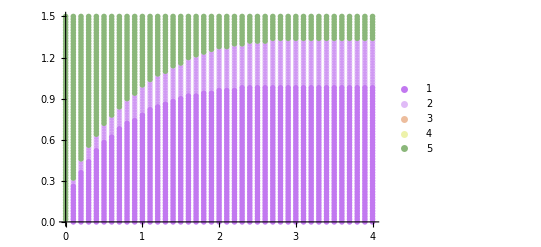

```mathematica
ListPlot[{y1,y2,y3,y4,y5},PlotLegends->Automatic,PlotMarkers->{•,8},PlotStyle->{{ColorData["Pastel",0]},{ColorData["Pastel",0],Opacity[0.5]},{ColorData["Pastel",1/3]},{ColorData["Pastel",2/3]},{ColorData[95,0]}}]
```

```mathematica
f1=Interpolation[z1];
f2=Interpolation[z2];
```

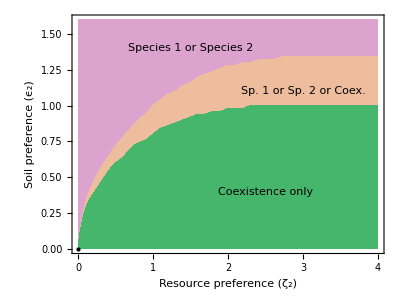

```mathematica
figA4b=RegionPlot[{y>f2[x],y<f2[x],y<f1[x]},{x,0,4},{y,0,1.6},PlotStyle->{RGBColor[0.8570441666666667, 0.6373188333333333, 0.8020406666666666],RGBColor[0.927848, 0.742785, 0.6151383333333333],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]},BoundaryStyle->None,Frame->True,FrameLabel->{"Resource preference (ζ_2)","Soil preference (ϵ_2)"},Axes->{False,False},LabelStyle->{FontSize->20,FontColor->Black},Epilog-> {{PointSize[Large],Point[{0,0}]},{Inset[Text[Style["Species 1 or Species 2",FontSize->13]],{1.5,1.4}],Inset[Text[Style["Sp. 1 or Sp. 2 or Coex. ",FontSize->13]],{3,1.1}],Inset[Text[Style["Coexistence only ",FontSize->13]],{2.5,0.4}]}},AspectRatio->0.75]
```

```mathematica
Export["\\\\wsl.localhost\\Debian\\home\\athma\\trait_cond_models\\paper_2\\images\\figA4b.jpg",figA4b];
```

### Competition coefficient - Quartic function of trait difference

```mathematica
ClearAll["α","β","f"]
```

#### Dynamics

```mathematica
Subscript[dN, 1]:=Subscript[N, 1](1-S^4/ω^4-(β Subscript[N, 1]+α Subscript[N, 2]));
Subscript[dN, 2]:=Subscript[N, 2](1-(S-ϵ)^4/ω^4-(α Subscript[N, 1]+β Subscript[N, 2]));
dS:=η(-S)Subscript[N, 1]+η(ϵ-S)Subscript[N, 2];
```

```mathematica
Jc:={{D[Subscript[dN, 1],Subscript[N, 1]],D[Subscript[dN, 1],Subscript[N, 2]],D[Subscript[dN, 1],S]},{D[Subscript[dN, 2],Subscript[N, 1]],D[Subscript[dN, 2],Subscript[N, 2]],D[Subscript[dN, 2],S]},{D[dS,Subscript[N, 1]],D[dS,Subscript[N, 2]],D[dS,S]}};
```

#### Phase space

```mathematica
pars={ω->1,σ->1,ν->1,η->1};
ϵs=Range[0,1.5,0.02];
nϵ=Length[ϵs];
ζs=Range[0,4,0.1];
nζ=Length[ζs];
```

```mathematica
eq=Array[,{nζ,nϵ}];
λ1=Array[,{nζ,nϵ}];
λ2=Array[,{nζ,nϵ}];
λ3=Array[,{nζ,nϵ}];
z1=Array[,{nζ,2}];
z2=Array[,{nζ,2}];
z3=Array[,{nζ,2}];
z4=Array[,{nζ,2}];
z5=Array[,{nζ,2}];
z6=Array[,{nζ,2}];
y1=Array[,{nϵ*nζ,2}];
y2=Array[,{nϵ*nζ,2}];
y3=Array[,{nϵ*nζ,2}];
y4=Array[,{nϵ*nζ,2}];
y5=Array[,{nϵ*nζ,2}];
```

```mathematica
eqCounts=List[0,0,0,0,0,0];
```

```mathematica
Do[
ch1=0;
ch2=0;
Do[
α=ν Exp[-ζ^4/(2 σ^4)]/.pars/.ζ->ζs[[j1]];
β=ν/.pars;
eq[[j1,j2]]=FullSimplify[Solve[(Subscript[dN, 1]/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]])==0&&(Subscript[dN, 2]/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]])==0&&(dS/.pars/.ϵ->ϵs[[j2]])==0&&Subscript[N, 1]>0&&Subscript[N, 2]>0,{Subscript[N, 1],Subscript[N, 2],S},Reals]];
If[Length[eq[[j1,j2]]]==3,
λ1[[j1,j2]]=Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2,2]]]]];
If[Length[eq[[j1,j2]]]==1,
λ1[[j1,j2]]=Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2]]]]];
λ2[[j1,j2]]=Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.{Subscript[N, 1]->1/β,Subscript[N, 2]->0,S->0}]];
λ3[[j1,j2]]=Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.{Subscript[N, 1]->0,Subscript[N, 2]->1/β,S->ϵs[[j2]]}]];

eqCounts[[Length[eq[[j1,j2]]]+1]]++;

If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]≥0&& λ3[[j1,j2]]≥0,y1[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]<0,y2[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]≥0,y3[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&& λ2[[j1,j2]]>=0&& λ3[[j1,j2]]<0,y4[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[(λ1[[j1,j2]]≥0||λ1[[j1,j2]]==Null[j1,j2])&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]<0,y5[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];

If[λ2[[j1,j2]]<0&&ch1==0,z1[[j1]]={ζs[[j1]],ϵs[[j2]]};ch1=1];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&&λ2[[j1,j2]]<0&&λ3[[j1,j2]]<0&&ch2==0,z2[[j1]]={ζs[[j1]],ϵs[[j2]]};ch2=1],

{j2,nϵ}],
{j1,nζ}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Solve::svars: Equations may not give solutions for all "solve" variables.

Eigenvalues::eival: Unable to find all roots of the characteristic polynomial.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

1 - coex only
2 - coex + s1 + s2
3 - s1
4 - s2
5 - s1 + s2 (priority effect)

```mathematica
eqCounts
```

{0,2579,0,537,0,0}

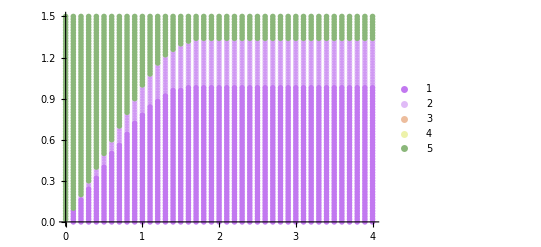

```mathematica
ListPlot[{y1,y2,y3,y4,y5},PlotLegends->Automatic,PlotMarkers->{•,8},PlotStyle->{{ColorData["Pastel",0]},{ColorData["Pastel",0],Opacity[0.5]},{ColorData["Pastel",1/3]},{ColorData["Pastel",2/3]},{ColorData[95,0]}}]
```

```mathematica
f1=Interpolation[z1];
f2=Interpolation[z2];
```

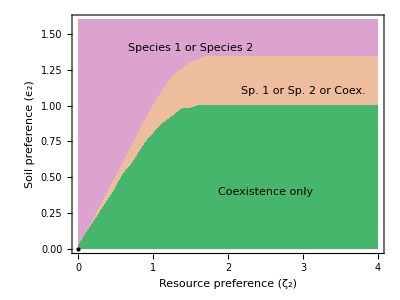

```mathematica
figA4c=RegionPlot[{y>f2[x],y<f2[x],y<f1[x]},{x,0,4},{y,0,1.6},PlotStyle->{RGBColor[0.8570441666666667, 0.6373188333333333, 0.8020406666666666],RGBColor[0.927848, 0.742785, 0.6151383333333333],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]},BoundaryStyle->None,Frame->True,FrameLabel->{"Resource preference (ζ_2)","Soil preference (ϵ_2)"},Axes->{False,False},LabelStyle->{FontSize->20,FontColor->Black},Epilog-> {{PointSize[Large],Point[{0,0}]},{Inset[Text[Style["Species 1 or Species 2",FontSize->13]],{1.5,1.4}],Inset[Text[Style["Sp. 1 or Sp. 2 or Coex. ",FontSize->13]],{3,1.1}],Inset[Text[Style["Coexistence only ",FontSize->13]],{2.5,0.4}]}},AspectRatio->0.75]
```

```mathematica
Export["\\\\wsl.localhost\\Debian\\home\\athma\\trait_cond_models\\paper_2\\images\\figA4c.jpg",figA4c];
```